# Comparação do Comportamento da impedância interna de condutores de linhas de transmissão aéreas

## Antonio Carlos Siqueira de Lima Escola Politécnica/UFRJ Julho de 2021

## Inicialização

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
SetOptions[{ListPlot, ListLogPlot, ListLogLogPlot, ListLogLinearPlot}, BaseStyle-> {FontFamily-> "Helvetica", 14}, ImageSize-> 600, Joined-> True, 
PlotStyle->{{Thick, Darker@Red},{Thick,Dashed,Darker@Green},{Thick, DotDashed,Darker@Blue},{Thick,Darker@Cyan},
{Thick, Black},
{Thick, Dashed, Darker@Magenta},
{Thick,DotDashed, Darker@Yellow}}, Axes-> False, Frame-> True];
```

```mathematica
<<LineCableParam2020`
```

### Constantes

```mathematica
μ=4.0*Pi*10^-7;
ϵ=8.854 10^-12;
```

### Definindo o vetor de frequências

usando espaçamento logaritmico entre as amostras de frequência

```mathematica
f = logspac[-2,5, 250];
```

### Expressões aproximadas

Para condutores cilindricos sólidos

```mathematica
Zapp1[Omega_, Rhoc_, rf_,  Mur_: 1, Mu_: (4.*Pi)/10^7] := 
 With[{Etac = N[Sqrt[(I*Omega*Mur*Mu)/Rhoc]]},
Etac Rhoc/(2 π rf)Coth[0.777 Etac rf]+0.356 Rhoc/(2 π rf)]
```

Para condutores cilindricos tubulares

```mathematica
Zapp2[Omega_, Rhoc_, rf_, ri_, Mur_: 1, Mu_: (4.*Pi)/10^7] := 
 With[{Etac = N[Sqrt[(I*Omega*Mur*Mu)/Rhoc]]},
Etac Rhoc/(2 π rf)Coth[Etac (rf-ri)]+ Rhoc/(2 π rf(rf+ri))]
```

## Condutor Bluejay

-Tipo do condutor: ACSR 1113 MCM 45/7 BLUEJAY
raio externo: 15,977 mm
raio interno:    8,702 mm
resistividade: 29,544 nΩ.m (2.9544e-8)

```mathematica
re= 15.977 10^-3;
ri = 8.702 10^-3;
ρ= 29.544 10^-9;
```

### Calculando as impedâncias

Zbj -- impedância do condutor Bluejay (cond. tubular)
Zbja -- idem mas considerando condutor cilindrico
Zbja1 --  impedância condutor cilindrico usando fórmulas aproximadas
Zbja2 -- impedância condutor cilindrico tubular usando fórmulas aproximadas

```mathematica
Zbj = ZintTubo[2π f, ρ,re,ri];
Zbja = Zin[2π f, ρ,re,1];
Zbja1=Zapp1[2π f, ρ,re];
Zbja2=Zapp2[2π f, ρ,re,ri];
```

Comparando as resistências

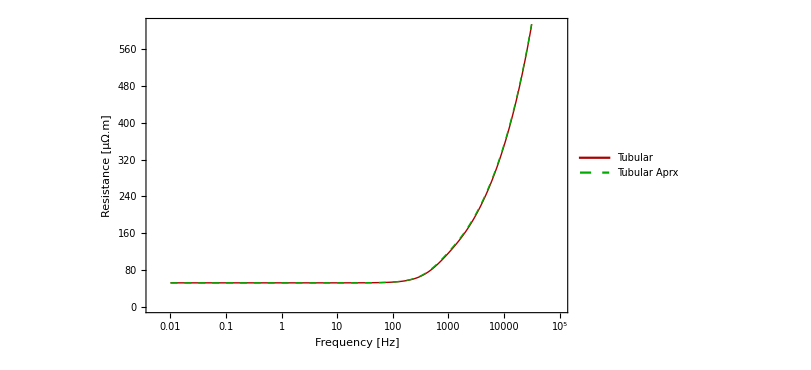

```mathematica
o1=ListLogLinearPlot[{
Transpose@{f,10^6 Re[Zbj]},
Transpose@{f,10^6Re[Zbja2]}
}, FrameLabel->{"Frequency [Hz]", "Resistance [μΩ.m]"},
PlotLegends->Placed[LineLegend[{"Tubular","Tubular Aprx" }],{.225,.785}]
]
```

```mathematica
Export["rbluejay.pdf", o1]
```

rbluejay.pdf

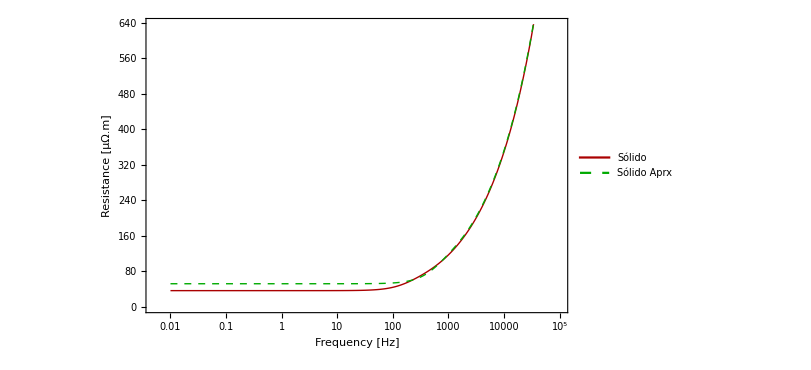

```mathematica
ListLogLinearPlot[{
Transpose@{f,10^6Re[Zbja]},
Transpose@{f,10^6Re[Zbja2]}
}, FrameLabel->{"Frequency [Hz]", "Resistance [μΩ.m]"},
PlotLegends->Placed[LineLegend[{  "Sólido","Sólido Aprx" }],{.225,.785}]
]
```

Comparando as indutâncias

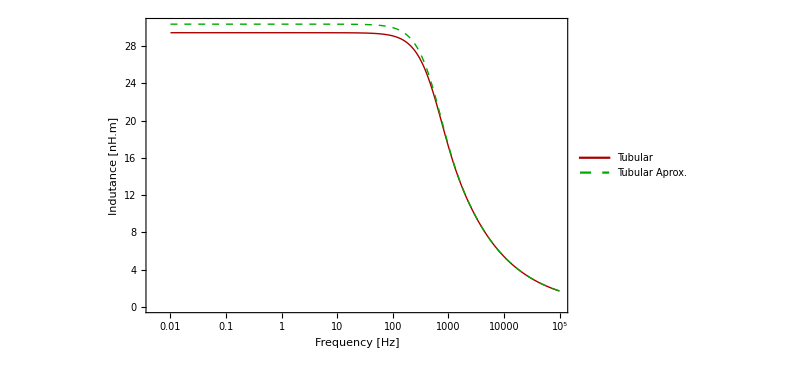

```mathematica
o2= ListLogLinearPlot[{Transpose@{f, 10^9Im[Zbj]/(2 π f)},Transpose@{f,10^9Im[Zbja2]/(2 π f)}}, FrameLabel->{"Frequency [Hz]", "Indutance [nH.m]"},PlotLegends->Placed[LineLegend[{"Tubular", "Tubular Aprox." }],{.25,.25}]]
```

```mathematica
Export["Lbluejay.pdf", o2]
```

Lbluejay.pdf

Comparando os erros relativos

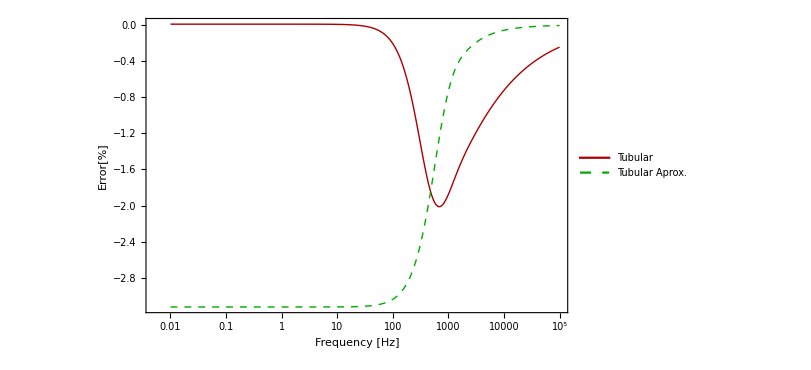

```mathematica
ListLogLinearPlot[{
Transpose@{f,100( Re[Zbj]-Re[Zbja2])/Re[Zbj]},
Transpose@{f,100( Im[Zbj]-Im[Zbja2])/Im[Zbj]}},
FrameLabel-> {"Frequency [Hz]", "Error[%]"},
PlotLegends->Placed[LineLegend[{"Tubular", "Tubular Aprox." }],{.225,.25}]]
```